```mathematica
(*Load Matte*)
AppendTo[$Path,NotebookDirectory[]];
<<Matte`
```

Matte package loaded. © 2017-2018 Jonas Einarsson (me@jonaseinarsson.se)

Released under the MIT License https://opensource.org/licenses/MIT

### Define basic multipoles

```mathematica
getStokeslet[i_,j_]:=delta[i,j]invr[1]+r[i]r[j]invr[3]
getStokesletP[j_]:=2r[j]invr[3]
laplacer[getStokeslet[idx[1],idx[2]]]-partialr[getStokesletP[idx[2]],idx[1]]//contract  (* check Stokes eq. satisfied *) 

getDipole[i_,j_,k_]:=partialr[getStokeslet[i,j],k]//contract
getRotlet[i_,j_,k_]:= 1/2getDipole[i,j,k]-1/2getDipole[i,k,j]//contract
getStresslet[i_,j_,k_]:= 1/2getDipole[i,j,k]+1/2getDipole[i,k,j]//contract
```

0

### Defining zeroth order flow fields

```mathematica
getUsquirmer0 [i_,p_]:= Module[{j}, j=getNewIndex[];
-2/3 p[i]+p[j](r[i]r[j]invr[5]-delta[i,j]invr[3]/3)
] (* Newtonian flow field for a neutral squirmer *)
getLinearFlow[i_,S_]:=Module[{j},j=getNewIndex[];
Γ*S[i,j]r[j]
] (* i is the index and S is the constant we use for our linear flow *) 

getUsquirmer0 [idx[1],p] //contract//prettyprint
partialr[getUsquirmer0 [idx[1],p],idx[1]]//contract//prettyprint (* check squirmer flow satisfies continuity *)
```

1/3 (-2-1/r^3) p_i+(p_j r_i r_j)/r^5

0

### Write down basic disturbance flows for sphere in Newtonian linear flows

```mathematica
getDisturbanceFlowStrain[i_,e_]:=Module[{j,k}, {j,k}=getNewIndex[2];
5/6 getStresslet[i,j,k]e[j,k]*Γ+1/12 laplacer[getStresslet[i,j,k]]e[j,k]*Γ//contract//renumberUnique
] (* disturbance flow for a particle in straining flow *) 
getDisturbanceFlowRotation[i_,o_]:=Module[{j,k}, {j,k}=getNewIndex[2];
1/2 getRotlet[i,j,k]o[j,k]*Γ//contract//renumberUnique
] (* disturbance flow for a particle in a vortical flow *) 

getDisturbanceFlowRotation[idx[1],o];
getLinearFlow[idx[1],o]+%/.invr[_]:>1 //contract(*check bc - evaluate at r=1. should be 0 cause no-slip. *)
getDisturbanceFlowStrain[idx[1],e];
getLinearFlow[idx[1],e]+%/.invr[_]:>1 //contract(*check bc - evaluate at r=1. should be 0 cause no-slip. *)
```

0

0

```mathematica
(* check that the disturbance flow from the external linear flow satisfies continuity *) 
partialr[getDisturbanceFlowStrain[idx[1],e],idx[1]]//contract//prettyprint 
partialr[getDisturbanceFlowRotation[idx[1],e],idx[1]]//contract//prettyprint
```

0

0

### Solution for flow around sphere in squirmer flow + linear flow by superposition

```mathematica
getuinfinity[i_]:=getLinearFlow[i,e]+getLinearFlow[i,o]  (* general linear flow can be decomposed into symmetric and antisymmetric part *) 
getudisturbance[i_]:=getDisturbanceFlowStrain[i,e] (* disturbance flow of a passive particle. we don't add the disturbance flow of the rotation because the particle is rotating. *)
getu[i_]:=getuinfinity[i]+getudisturbance[i]+getUsquirmer0[i,p]//contract//renumberUnique
getu[idx[1]]//contract//prettyprint (* print out velocity to compare to what is known *) 
getu[idx[1]]/.invr[_]:>1//contract //prettyprint(* Check no-slip condition. should recover squirmer BC + rigid body rotation *)
```

1/3 (-2-1/r^3) p_i+(p_j r_i r_j)/r^5+(Γ-Γ/r^5) r_j e_(i,j)+5/2 (1/r^7-1/r^5) Γ r_i r_j r_k e_(j,k)+Γ r_j o_(i,j)

-p_i+p_j r_i r_j+Γ r_j o_(i,j)

### Defining gradients of flow at infinity

```mathematica
getGradientInfinity[i_,j_] := partialr[getuinfinity[i],j]//contract//renumberUnique
getStrainInfinity[i_,j_]:=1/2getGradientInfinity[i,j]+1/2getGradientInfinity[j,i]//contract//renumberUnique
getGradientInfinity[idx[1],idx[2]]//prettyprint
getStrainInfinity[idx[1],idx[2]]//prettyprint
```

Γ e_(i,j)+Γ o_(i,j)

Γ e_(i,j)

### Defining gradients of zeroth order flow

```mathematica
getGradient[i_,j_] := partialr[getu[i],j]//contract//renumberUnique
getStrain [i_,j_]:=1/2getGradient[i,j]+1/2getGradient[j,i]//contract//renumberUnique
```

### Compute s_ij at infinity

```mathematica
2*(getGradientInfinity[idx[1],idx[2]]*getStrainInfinity[idx[2],idx[3]]+getGradientInfinity[idx[3],idx[2]]*getStrainInfinity[idx[2],idx[1]])//contract//renumber//prettyprint
```

4 Γ^2 e_(i,l) e_(k,l)+2 Γ^2 e_(k,l) o_(i,l)+2 Γ^2 e_(i,l) o_(k,l)

### Defining auxiliary flow

```mathematica
(*Auxiliary flow is that of a single particle translating at a velocity V in quiescent fluid*)
getAuxG [i_,j_]:=3/4(invr[1]+1/3invr[3])delta[i,j]+3/4(invr[3]-invr[5])r[i]r[j]; (* transfer matrix *) 
getAuxV[i_] :=Module[{j},j=getNewIndex[];
getAuxG [i,j]V[j]
] (* auxillary flow field, u *) 
getAuxPartialG[i_,j_,k_] :=partialr[getAuxG[i,k],j]
getAuxV[idx[1]]//contract//prettyprint (* prettyprint to make sure G is input correctly *)
```

1/4 (1/r^3+3/r) V_i+3/4 (-1/r^5+1/r^3) r_i r_j V_j

### Computing O(Wi) term from O(1) terms

```mathematica
(* each of these terms is from pencil-paper application of the reciprocal theorem *) 
term1=Module[{i,j,k},i=idx[1];j=idx[2];k=getNewIndex[];
-2getu[k]partialr[getStrain[i,j],k]//contract
];
term2=Module[{i,j,k},i=idx[1];j=idx[2];k=getNewIndex[];
2getGradient[i,k]getStrain[k,j]+2getGradient[j,k]getStrain[k,i]//contract
];
term3 = Module[{i,j,k},i=idx[1];j=idx[2];k=getNewIndex[];
-2 getGradientInfinity[i,k]getStrainInfinity[k,j] -2   getGradientInfinity[j,k]getStrainInfinity[k,i]//contract
];
sij= (1-β)(term1+term2+term3)//contract;
Length[sij]
```

254

### Calculating integrands

```mathematica
(*Volume integral of *)
G = getAuxPartialG[idx[1],idx[2],idx[-1]]//contract;
integrand=-G sij//contract;
fluidVolumeIntegral[%]/.idx[-1]->idx[1]//contract//renumber//prettyprint (* compute volume integral to recover velocity *)
```

2 π (-1+β) Γ p_j e_(i,j)

### Try Anni’s derivation of the squirmer velocity

```mathematica
getσE[i_,j_] :=Module[{k},k=getNewIndex[];
(1-β)*-2*(getu[k]*partialr[getStrain[i,j],k]-getGradient[i,k]getStrain[k,j]-getGradient[j,k]getStrain[k,i])
]
term1=Module[{i,j},i=idx[1];j=getNewIndex[];
1/6/π*(getσE[i,j]r[j])//contract//unitsphereIntegral//contract
];
term2=Module[{i,j,k},i=idx[1];j=getNewIndex[];k=getNewIndex[];
-1/6/π*(getAuxG[i,j]partialr[getσE[k,j],k])//contract//fluidVolumeIntegral//contract
];

term1//prettyprint
term2//prettyprint
(term1-term2)//prettyprint (* subtract term 2 since fluidVolumeIntegral is negative of the integral we typically write *)
```

4/3 (-1+β) Γ p_j e_(i,j)

(-1+β) Γ p_j e_(i,j)

1/3 (-1+β) Γ p_j e_(i,j)

```mathematica
%*6*π
```

2 π (-1+β) Γ p_j e_(i,j)

This integral is off by a factor of 7 from the result from Eric’s formula above.

### Rotation rate

```mathematica
term1=Module[{i,j,m,n},m=idx[1];j=getNewIndex[];i=getNewIndex[];n=getNewIndex[];
1/8/π*(eps[m,n,i]r[n]getσE[i,j]r[j])//contract//unitsphereIntegral//contract
];
term2=Module[{i,j,m,n},m=idx[1];j=getNewIndex[];i=getNewIndex[];n=getNewIndex[];
-1/8/π*(eps[m,n,j]r[n]invr[3]partialr[getσE[i,j],i])//contract//fluidVolumeIntegral//contract
];

term1//prettyprint
term2//prettyprint
(term1-term2)//prettyprint (* subtract term 2 since fluidVolumeIntegral is negative of the integral we typically write *)
```

0

11/60 (-1+β) Γ^2 e_(j,k) e_(j,l) ϵ_(i,k,l)

-11/60 (-1+β) Γ^2 e_(j,k) e_(j,l) ϵ_(i,k,l)

### Consistency checks to add

- Does 0th order satisfy Stokes equation, BCs, continuity
- Does solution satisfy Lorentz Reciprocal theorem

## Visualize neutral flow

### Lab frame

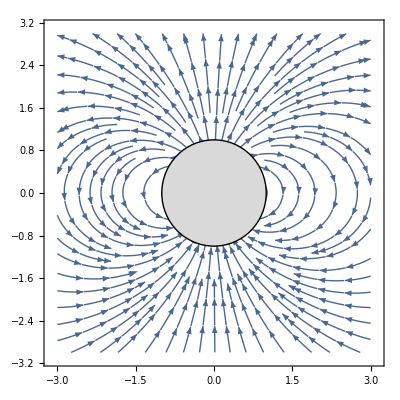

```mathematica
Show[
StreamPlot[{x*z/(x^2+z^2)^(5/2),-1/3/(x^2+z^2)^(3/2)+z^2/(x^2+z^2)^(5/2)},{x,-3,3},{z,-3,3}],
Graphics[{LightGray,Disk[{0,0},1]}],
Graphics[{Black,Circle[{0,0},1]}]
]
```

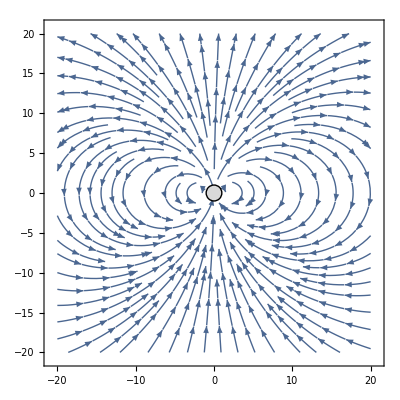

```mathematica
Show[
StreamPlot[{x*z/(x^2+z^2)^(5/2),-1/3/(x^2+z^2)^(3/2)+z^2/(x^2+z^2)^(5/2)},{x,-20,20},{z,-20,20}],
Graphics[{LightGray,Disk[{0,0},1]}],
Graphics[{Black,Circle[{0,0},1]}]
]
```

### Co-moving frame

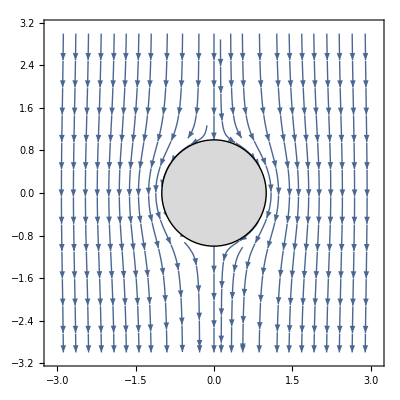

```mathematica
Show[
StreamPlot[{x*z/(x^2+z^2)^(5/2),-1/3/(x^2+z^2)^(3/2)+z^2/(x^2+z^2)^(5/2)-2/3},{x,-3,3},{z,-3,3}],
Graphics[{LightGray,Disk[{0,0},1]}],
Graphics[{Black,Circle[{0,0},1]}]
]
```

### Gradient of neutral squirmer

```mathematica
getUsquirmer0 [idx[1],p] //contract//prettyprint
```

1/3 (-2-1/r^3) p_i+(p_j r_i r_j)/r^5

```mathematica
prettyprint[contract[partialr[getUsquirmer0[idx[1],p],idx[2]]]]
```

(p_j r_i)/r^5+(p_i r_j)/r^5-(5 p_k r_i r_j r_k)/r^7+(p_k r_k δ_(i,j))/r^5